```mathematica
(* set up the Levy alpha-stable SDE *)
α=1;
(* drift *)
f[x_] := If[Abs[x]≤3π,5Sin[x/2],-5 Sign[x]]
(* constant diffusion *)
g=0.25;
```

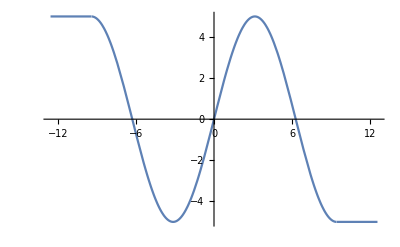

```mathematica
Plot[f[x],{x,-4π,4π}]
```

```mathematica
Integrate[1/(2 π L) Exp[-I j x/L] f[x],{x,-L π,L π},Assumptions->{L∈Integers,L>0}]
```

Piecewise[{{-(5 ⅈ ⅇ^(-ⅈ j π-(3 ⅈ j π)/L) (-4 ⅇ^(ⅈ j π) j^2+4 ⅇ^((3 ⅈ j π)/L) j^2+4 ⅇ^(2 ⅈ j π+(3 ⅈ j π)/L) j^2-4 ⅇ^(ⅈ j π+(6 ⅈ j π)/L) j^2+ⅇ^(ⅈ j π) L^2-ⅇ^((3 ⅈ j π)/L) L^2-ⅇ^(2 ⅈ j π+(3 ⅈ j π)/L) L^2+ⅇ^(ⅈ j π+(6 ⅈ j π)/L) L^2+8 ⅇ^(ⅈ j π+(3 ⅈ j π)/L) j^2 Cos[(3 j π)/L]))/(2 j (4 j^2-L^2) π), L>3}, {(10 ⅈ (-L Cos[(L π)/2] Sin[j π]+2 j Cos[j π] Sin[(L π)/2]))/((4 j^2-L^2) π), True}}]

```mathematica
FullSimplify[-1/(2 j (4 j^2-L^2) π)5 ⅈ ⅇ^(-ⅈ j π-(3 ⅈ j π)/L) (-4 ⅇ^(ⅈ j π) j^2+4 ⅇ^((3 ⅈ j π)/L) j^2+4 ⅇ^(2 ⅈ j π+(3 ⅈ j π)/L) j^2-4 ⅇ^(ⅈ j π+(6 ⅈ j π)/L) j^2+ⅇ^(ⅈ j π) L^2-ⅇ^((3 ⅈ j π)/L) L^2-ⅇ^(2 ⅈ j π+(3 ⅈ j π)/L) L^2+ⅇ^(ⅈ j π+(6 ⅈ j π)/L) L^2+8 ⅇ^(ⅈ j π+(3 ⅈ j π)/L) j^2 Cos[(3 j π)/L])]
```

-(5 ⅈ (Cos[j π]-(L^2 Cos[(3 j π)/L])/(-4 j^2+L^2)))/(j π)

```mathematica
-(5 ⅈ (Cos[j π]-(L^2 Cos[(3 j π)/L])/(-4 j^2+L^2)))/(j π)
```

```mathematica
Limit[-(5 ⅈ (Cos[j π]-(L^2 Cos[(3 j π)/L])/(-4 j^2+L^2)))/(j π),j->L/2]
```

-(5 ⅈ (3 π+4 Cos[(L π)/2]))/(2 L π)

```mathematica
Limit[-(5 ⅈ (Cos[j π]-(L^2 Cos[(3 j π)/L])/(-4 j^2+L^2)))/(j π),j->-L/2]
```

(5 ⅈ (3 π+4 Cos[(L π)/2]))/(2 L π)

```mathematica
(5 ⅈ (L π-Sin[L π]))/(2 L π)
```

```mathematica
(5 ⅈ (L π-Sin[L π]))/(2 L π) /. L->1
```

(5 ⅈ)/2

```mathematica
Limit[-(5 ⅈ (Cos[j π]-(L^2 Cos[(3 j π)/L])/(-4 j^2+L^2)))/(j π),j->-L/2]
```

(5 ⅈ (3 π+4 Cos[(L π)/2]))/(2 L π)

```mathematica
(5 ⅈ (3 π+4 Cos[(L π)/2]))/(2 L π) /. L->1
```

(15 ⅈ)/2

```mathematica
Limit[-(5 ⅈ (Cos[j π]-(L^2 Cos[(3 j π)/L])/(-4 j^2+L^2)))/(j π),j->L/2]
```

-(5 ⅈ (3 π+4 Cos[(L π)/2]))/(2 L π)

```mathematica
ntraj=500;
nsamp=1;
numsteps=1000;
tvec=Table[j*dt,{j,0,numsteps}];
dt = 0.01;
mcsol=Table[0,{numsteps+1},{ntraj}];
mcsol[[1,1;;ntraj]]=RandomVariate[NormalDistribution[0,5],ntraj];
For[i=1,i≤numsteps,i+=1,
mcsol[[i+1,1;;ntraj]] =mcsol[[i,1;;ntraj]]+ dt*Map[f,mcsol[[i,1;;ntraj]]] +  RandomVariate[StableDistribution[1,α,0.0,0.0,dt g],ntraj];
];
```

```mathematica
Max[mcsol[[1,1;;ntraj]]]
```

14.9322

```mathematica
FourierTransform[PDF[NormalDistribution[0,5],x],x,s,FourierParameters->{1,1}]
```

ⅇ^(-(25 s^2)/2)

```mathematica
Export["mcsolnewdblwell2.csv",mcsol]
```

mcsolnewdblwell2.csv